```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
pr[list_,c_]:=Table[list⟦i⟧⟦c⟧,{i,1,Length[list]}]
```

## Import data

```mathematica
Header="RecData_tau0.1";
```

#### Get the number of files to expect

```mathematica
numberF=Length[Import[Header]];
```

#### Predictor data

```mathematica
predData={};
For[i=1,i≤numberF/2,++i,AppendTo[predData,Import[Header<>"/PCF"<>ToString[i]<>".csv"]]]
```

```mathematica
predLst=Table[{predData⟦1⟧⟦j⟧⟦1⟧,Sum[predData⟦i⟧⟦j⟧⟦2⟧,{i,1,Length[predData]}]/Length[predData]},{j,1,Length[predData⟦1⟧]}];
```

```mathematica
predSig=Table[{predData⟦1⟧⟦j⟧⟦1⟧,(Sum[(predData⟦i⟧⟦j⟧⟦2⟧-predLst⟦j⟧⟦2⟧)^2,{i,1,Length[predData]}]/Length[predData])^(1/2)},{j,1,Length[predData⟦1⟧]}];
```

#### Gradient data

```mathematica
gradData={};
For[i=1,i≤numberF/2,++i,AppendTo[gradData,Import[Header<>"/GCF"<>ToString[i]<>".csv"]]]
```

```mathematica
gradLst=Table[{gradData⟦1⟧⟦j⟧⟦1⟧,Sum[gradData⟦i⟧⟦j⟧⟦2⟧,{i,1,Length[gradData]}]/Length[gradData]},{j,1,Length[gradData⟦1⟧]}];
```

```mathematica
gradSig=Table[{gradData⟦1⟧⟦j⟧⟦1⟧,(Sum[(gradData⟦i⟧⟦j⟧⟦2⟧-gradLst⟦j⟧⟦2⟧)^2,{i,1,Length[gradData]}]/Length[gradData])^(1/2)},{j,1,Length[gradData⟦1⟧]}];
```

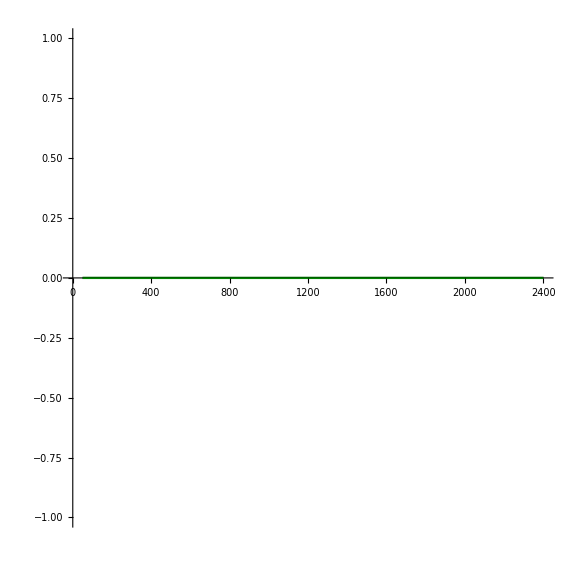

```mathematica
ListLinePlot[{predLst,gradLst},PlotStyle->{Purple,Green},ImageSize->Large,AspectRatio->1]
```

```mathematica
Quiet[Needs["ErrorBarPlots`"]]
```

#### Create predictor error plot data

```mathematica
Clear[predCF]
predCF=Partition[Riffle[pr[predLst,2],pr[predSig,2]],2];
```

#### Create gradient error plot data

```mathematica
Clear[gradCF]
gradCF=Partition[Riffle[pr[gradLst,2],pr[gradSig,2]],2];
```

#### Create graph

```mathematica
ts=Table[{i,gradLst⟦i⟧⟦1⟧},{i,1,Length[gradLst],4}];
tickSpecs={ts,Automatic};
```

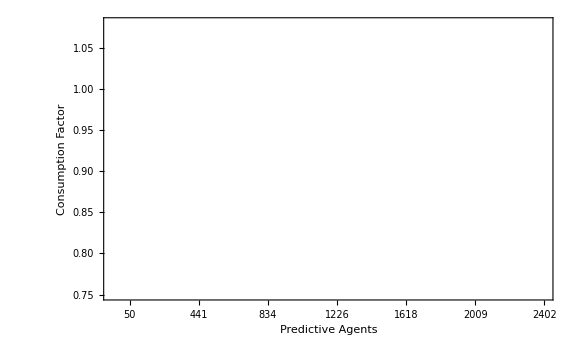

```mathematica
ErrorListPlot[{predCF,gradCF},Joined->True,Frame->True,FrameTicks->tickSpecs,PlotRange->{0.75,1.08},FrameLabel->{Style["Predictive Agents",12,FontFamily->"Arial"],Style["Consumption Factor",12,FontFamily->"Arial"]},PlotStyle->{Purple,Green},ImageSize->Large]
```